```mathematica
b[n_] := 3 * n + 1
```

```mathematica
a[n_] := 2*n + 1
```

```mathematica
collatz[n_] := If[EvenQ[n], n/2, 3n + 1]
```

```mathematica
totient[n_Integer] := Length[ResourceFunction["CoprimeIntegerList"][n]]
triangle[n_Integer] := n(n+1)/2
```

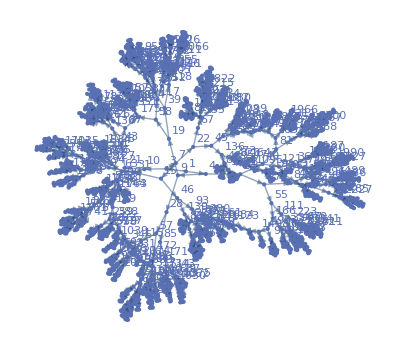

```mathematica
NestGraph[n|->{a[n], b[n]}, 1,10, VertexLabels->Automatic]
```

```mathematica
ResourceFunction["NestGraphTagged"][n↦{a[n], b[n]},{0},7,"StateLabeling"->True,PlotLegends->TraditionalForm/@{a[n],b[n]}]
```

-Graphics-

```mathematica
Graph3D[ResourceFunction["NestGraphTagged"][n↦{n+7,n+11},{0},20],VertexSize->.5,VertexStyle->Darker[RGBColor[0.9215683283650572, 0.9294118431048657, 0.9411764788496759, 1],.25]]
```

-Graphics3D-

```mathematica
With[{g=ResourceFunction["GraphRemoveLooseEnds"][ResourceFunction["NestGraphTagged"][n|->{2 n+1,3 n+1},{0},8,"StateLabeling"->True],All]},Graph[g,EdgeStyle->Catenate[EdgeList@Subgraph[g,PathGraph[First@FindPath[g,#,175],DirectedEdges->True]]/.e:DirectedEdge[_,_,t_]:>e->Directive[{RGBColor[0.91, 0.16379999999999995, 0., 1],RGBColor[0.08499999999999998, 0.39100000000000024, 0.85, 1]}[[t]],Thickness[0.02]]&/@{3,4}]
]
]
```

-Graphics-

```mathematica
SortBy[Graph[#,GraphLayout->"SpringElectricalEmbedding",ImageSize->{Automatic,UpTo[100]}]&/@WeaklyConnectedGraphComponents[EdgeDelete[Graph[With[{g=ResourceFunction["NestGraphTagged"][n↦{3 n,Floor[n/2]},{1},10,"StateLabeling"->True]},Subgraph[g,VertexList[Flatten[FindCycle[UndirectedGraph[g],{4},All]]]]]],{DirectedEdge[5,2,2],DirectedEdge[81,40,2],DirectedEdge[91,45,2],DirectedEdge[29,14,2],DirectedEdge[3,1,2],DirectedEdge[9,4,2]}]],Min[VertexList[#]]&]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
funcs = {a[n], b[n]}
```

{1+2 n,1+3 n}

```mathematica
ResourceFunction["NestGraphTagged"][n↦{totient[n], n - totient[n] },{1138},20,"StateLabeling"->True,PlotLegends->TraditionalForm/@{totient[n], common[n]}]
```

-Graphics-

interesting property with totient and sharing a common factor--eventually all can devolve to a sequence of powers of 2???? conjecture--possible lower bound for hitting a certain power of 2 that seems surprisingly long
https://math.stackexchange.com/questions/2600457/finding-all-n-for-which-phin-is-power-of-2

```mathematica
ResourceFunction["NestGraphTagged"][n↦{a[n], b[n]},{1/Sqrt[2] + ⅈ/Sqrt[2]},3,"StateLabeling"->True,PlotLegends->TraditionalForm/@{a[n], b[n]}]
```

-Graphics-

```mathematica
ResourceFunction["NestGraphTagged"][n↦{3n-13, 4n-1},{1},5,"StateLabeling"->True,PlotLegends->TraditionalForm/@{a[n], b[n]}]
```

-Graphics-

```mathematica
ResourceFunction["NestGraphTagged"][n↦{n^2,Conjugate[n] * ⅇ^(ⅈ*3Pi/7)},{1/Sqrt[2]+ⅈ/Sqrt[2]},10,"StateLabeling"->True,PlotLegends->TraditionalForm/@{n^2,Conjugate[n] * ⅇ^(ⅈ*3Pi/7)}]
```

-Graphics-

```mathematica
ResourceFunction["NestGraphTagged"][n↦{Gamma[n], LaplaceTransform[b[t], t, n]},{6-ⅈ},3,"StateLabeling"->True,PlotLegends->TraditionalForm/@{Gamma[n], LaplaceTransform[b[t], t, n]}]
```

-Graphics-

```mathematica
ResourceFunction["NestGraphTagged"][n↦{Fibonacci[n], 4n-1},{1},4,"StateLabeling"->True,PlotLegends->TraditionalForm/@{a[n], b[n]}]
```

-Graphics-

```mathematica
ResourceFunction["NestGraphTagged"][n↦{2n, n+5},{1},7,"StateLabeling"->True,PlotLegends->TraditionalForm/@{2n, n+5}]
```

-Graphics-